Simplify with 2 prey

```mathematica
VarTablefunc[{prey1_,prey2_,diff_}] := (
VarZTable=Table[
nprey = 12;
(*EX = {-15.5,-17.5,-15.6,-15.5,-14.3,-15.4,-16.0,-17.0,-15.8,-13.3,-17.5,-16.2};*)
EX = {-15.66,-15.66,-15.66,-15.66,-15.66,-15.66,-15.66+diff,-15.66+diff,-15.66,-15.66,-15.66,-15.66};
VarX = {1,1,1,1,1,1,1,1,1,1,1,1};
(*VarX = {0.5,0.5,0.5,0.5,0.5,0.5,0.25,1.21,0.5,0.5,0.5,0.5};*)
Dparam =Table[1,{nprey}];
Dparam[[prey1]] = a;
Dparam[[prey2]] = a;

a0 = Total[Dparam];
Ep = N[Dparam/a0];
Varp = N[Table[(Dparam[[i]]*(a0-Dparam[[i]]))/(a0^2*(a0+1)),{i,1,nprey}]];
Covp = N[Table[(-Dparam[[i]]*Dparam[[j]])/(a0^2*(a0+1))Boole[i ≠ j],{i,1,nprey},{j,1,nprey}]];
VarZ = N[Sum[Varp[[i]]*VarX[[i]] + Ep[[i]]^2*VarX[[i]] + EX[[i]]^2*Varp[[i]] + Sum[Covp[[i]][[j]]*EX[[i]]*EX[[j]]Boole[i ≠ j],{j,1,nprey}],{i,1,nprey}]];
propi = a/a0;
{propi,VarZ},
{a,1,1000,1}];
VarXTable = Table[{VarZTable[[i]][[1]],(λ*VarZTable[[i]][[2]])/2},{λ,0,1,0.1},{i,1,Length[VarZTable]}];
Return[{VarZTable,VarXTable}];
)
```

{A (Dotted),-15.66,1}

{B (Dashed),-15.66,1}

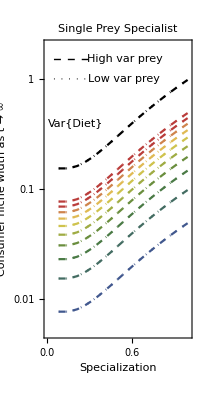
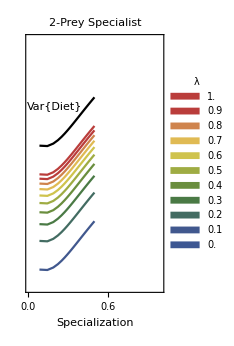
-Graphics--Graphics--Graphics3D-
-Graphics3D-
-Graphics3D-

```mathematica
prey1 = 7;
prey2 = 8;
diff = 0;
VarA = VarTablefunc[{prey1,prey1,diff}];VarZTableA = VarA[[1]];VarXTableA = VarA[[2]];
VarB = VarTablefunc[{prey2,prey2,diff}];VarZTableB = VarB[[1]];VarXTableB = VarB[[2]];
VarAB = VarTablefunc[{prey1,prey2,diff}];VarZTableAB = VarAB[[1]];VarXTableAB = VarAB[[2]];
{"A (Dotted)",EX[[prey1]],VarX[[prey1]]}
{"B (Dashed)",EX[[prey2]],VarX[[prey2]]}

MultipleSpecialistPlotdiff0 = 
Row[{
Show[{

ListLogPlot[VarZTableB,PlotStyle->Directive[{Black,Dashed}],PlotRange->{{0,1},{0.005,2}},Joined->True,AspectRatio->2,FrameLabel->{"Specialization","Consumer niche width as t → ∞"},Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},Epilog->Style[Text["Var{Diet}",{0.2,Log@0.4}],12],PlotLabel->"Single Prey Specialist"],
Table[
ListLogPlot[VarXTableB[[i+1]],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->Directive[Dashed,ColorData["DarkRainbow",i/10]],Joined->True],{i,1,10,1}],

ListLogPlot[VarZTableA,PlotStyle->Directive[{Black,Dotted}],PlotRange->{{0,1},{0.005,2}},Joined->True,Epilog->Style[Text["Var{Z}",{0.15,Log@0.3}],12]],
Table[
ListLogPlot[VarXTableA[[i+1]],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->Directive[Dotted,ColorData["DarkRainbow",i/10]],Joined->True],{i,1,10,1}],

Graphics[{Thick,Dashed,Line[{{0.05,Log@1.5},{0.3,Log@1.5}}]}],
Graphics[{Thick,Dotted,Line[{{0.05,Log@1},{0.3,Log@1}}]}],

Graphics[Text[Style["High var prey"],{0.55,Log@1.5}]],
Graphics[Text["Low var prey",{0.54,Log@1}]]

},ImageSize->200],

Show[{
ListLogPlot[VarZTableAB,Frame->True,PlotStyle->Black,PlotRange->{{0,1},{0.005,2}},Joined->True,AspectRatio->2,FrameLabel->{"Specialization",""},FrameTicks->{{None,None},{Automatic,None}},Epilog->Style[Text["Var{Diet}",{0.2,Log@0.4}],12],PlotLabel->"2-Prey Specialist"],
ListLogPlot[VarXTableAB,PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->"DarkRainbow",PlotLegends->SwatchLegend[Table[λ,{λ,0,1,0.1}],LegendLabel->"λ",LegendFunction->(#&),LegendMargins->1,LegendLayout->{"ReversedColumn",1}],Joined->True]
},ImageSize->173],
,"",
Column[{
prey1 = 7;
prey2 = 8;
DparamEx0 =Table[1,{nprey}];
Plot3D[PDF[MarginalDistribution[DirichletDistribution[DparamEx0[[1;;nprey-1]]],{prey1,prey2}],{x,y}],{x,0,1},{y,0,1},PlotRange->All,Mesh->None,Axes->{Automatic,Automatic,None},ColorFunction->"LightTemperatureMap",ImageSize->140],
DparamEx1 =Table[1,{nprey}];
DparamEx1[[prey1]] = 5;
DparamEx1[[prey2]] = 5;
Plot3D[PDF[MarginalDistribution[DirichletDistribution[DparamEx1[[1;;nprey-1]]],{prey1,prey2}],{x,y}],{x,0,1},{y,0,1},PlotRange->All,Mesh->None,Axes->{Automatic,Automatic,None},ColorFunction->"LightTemperatureMap",ImageSize->140],
DparamEx2 =Table[1,{nprey}];
DparamEx2[[prey1]] = 100;
DparamEx2[[prey2]] = 100;
Plot3D[PDF[MarginalDistribution[DirichletDistribution[DparamEx2[[1;;nprey-1]]],{prey1,prey2}],{x,y}],{x,0,1},{y,0,1},PlotRange->All,Mesh->None,Axes->{Automatic,Automatic,None},ColorFunction->"LightTemperatureMap",ImageSize->140]
}]
}," "]
```

```mathematica
offset = 1/VarZTableA[[All,2]]
```

{6.5,6.5,6.17647,5.71429,5.23077,4.78125,4.38462,4.04255,3.75,3.5,3.28571,3.10112,2.94118,2.80172,2.67939,2.57143,2.47561,2.39011,2.31343,2.24434,2.18182,2.125,2.07317,2.02572,1.98214,1.94199,1.90488,1.8705,1.83857,1.80882,1.78107,1.7551,1.73077,1.70792,1.68643,1.66617,1.64706,1.62899,1.61188,1.59567,1.58028,1.56565,1.55172,1.53846,1.52581,1.51374,1.50219,1.49115,1.48058,1.47045,1.46073,1.4514,1.44244,1.43382,1.42553,1.41755,1.40986,1.40244,1.39528,1.38838,1.3817,1.37525,1.36902,1.36298,1.35714,1.35149,1.346,1.34069,1.33553,1.33053,1.32567,1.32095,1.31637,1.31192,1.30758,1.30337,1.29927,1.29528,1.29139,1.2876,1.28391,1.28032,1.27681,1.27339,1.27005,1.26679,1.26361,1.2605,1.25747,1.25451,1.25161,1.24878,1.24601,1.2433,1.24065,1.23805,1.23552,1.23303,1.2306,1.22822,1.22588,1.22359,1.22135,1.21916,1.217,1.21489,1.21282,1.21079,1.20879,1.20683,1.20491,1.20303,1.20118,1.19936,1.19758,1.19582,1.1941,1.19241,1.19074,1.18911,1.1875,1.18592,1.18437,1.18284,1.18133,1.17986,1.1784,1.17697,1.17556,1.17417,1.17281,1.17146,1.17014,1.16884,1.16756,1.16629,1.16505,1.16382,1.16261,1.16142,1.16025,1.15909,1.15795,1.15683,1.15572,1.15463,1.15355,1.15249,1.15144,1.15041,1.14939,1.14838,1.14739,1.14641,1.14544,1.14449,1.14355,1.14262,1.1417,1.1408,1.1399,1.13902,1.13815,1.13729,1.13644,1.1356,1.13477,1.13395,1.13314,1.13234,1.13155,1.13077,1.13,1.12923,1.12848,1.12773,1.127,1.12627,1.12555,1.12484,1.12414,1.12344,1.12275,1.12207,1.1214,1.12073,1.12008,1.11942,1.11878,1.11814,1.11751,1.11689,1.11627,1.11566,1.11506,1.11446,1.11387,1.11328,1.1127,1.11213,1.11156,1.111,1.11044,1.10989,1.10934,1.1088,1.10827,1.10774,1.10721,1.10669,1.10618,1.10567,1.10517,1.10467,1.10417,1.10368,1.10319,1.10271,1.10224,1.10176,1.1013,1.10083,1.10037,1.09992,1.09947,1.09902,1.09857,1.09814,1.0977,1.09727,1.09684,1.09642,1.096,1.09558,1.09517,1.09476,1.09435,1.09395,1.09355,1.09315,1.09276,1.09237,1.09199,1.0916,1.09122,1.09085,1.09047,1.0901,1.08974,1.08937,1.08901,1.08865,1.0883,1.08794,1.08759,1.08725,1.0869,1.08656,1.08622,1.08588,1.08555,1.08522,1.08489,1.08456,1.08424,1.08392,1.0836,1.08328,1.08297,1.08266,1.08235,1.08204,1.08174,1.08144,1.08114,1.08084,1.08054,1.08025,1.07996,1.07967,1.07938,1.0791,1.07881,1.07853,1.07825,1.07797,1.0777,1.07743,1.07715,1.07688,1.07662,1.07635,1.07609,1.07583,1.07557,1.07531,1.07505,1.07479,1.07454,1.07429,1.07404,1.07379,1.07355,1.0733,1.07306,1.07282,1.07258,1.07234,1.0721,1.07186,1.07163,1.0714,1.07117,1.07094,1.07071,1.07048,1.07026,1.07003,1.06981,1.06959,1.06937,1.06915,1.06894,1.06872,1.06851,1.0683,1.06808,1.06787,1.06767,1.06746,1.06725,1.06705,1.06684,1.06664,1.06644,1.06624,1.06604,1.06584,1.06565,1.06545,1.06526,1.06507,1.06487,1.06468,1.06449,1.0643,1.06412,1.06393,1.06375,1.06356,1.06338,1.0632,1.06302,1.06284,1.06266,1.06248,1.0623,1.06213,1.06195,1.06178,1.0616,1.06143,1.06126,1.06109,1.06092,1.06075,1.06059,1.06042,1.06026,1.06009,1.05993,1.05976,1.0596,1.05944,1.05928,1.05912,1.05896,1.05881,1.05865,1.05849,1.05834,1.05818,1.05803,1.05788,1.05773,1.05758,1.05743,1.05728,1.05713,1.05698,1.05683,1.05669,1.05654,1.0564,1.05625,1.05611,1.05596,1.05582,1.05568,1.05554,1.0554,1.05526,1.05512,1.05499,1.05485,1.05471,1.05458,1.05444,1.05431,1.05417,1.05404,1.05391,1.05378,1.05365,1.05351,1.05339,1.05326,1.05313,1.053,1.05287,1.05275,1.05262,1.05249,1.05237,1.05224,1.05212,1.052,1.05187,1.05175,1.05163,1.05151,1.05139,1.05127,1.05115,1.05103,1.05091,1.0508,1.05068,1.05056,1.05045,1.05033,1.05022,1.0501,1.04999,1.04988,1.04976,1.04965,1.04954,1.04943,1.04932,1.04921,1.0491,1.04899,1.04888,1.04877,1.04866,1.04856,1.04845,1.04834,1.04824,1.04813,1.04803,1.04792,1.04782,1.04771,1.04761,1.04751,1.0474,1.0473,1.0472,1.0471,1.047,1.0469,1.0468,1.0467,1.0466,1.0465,1.0464,1.04631,1.04621,1.04611,1.04602,1.04592,1.04583,1.04573,1.04564,1.04554,1.04545,1.04535,1.04526,1.04517,1.04507,1.04498,1.04489,1.0448,1.04471,1.04462,1.04453,1.04444,1.04435,1.04426,1.04417,1.04408,1.04399,1.0439,1.04382,1.04373,1.04364,1.04356,1.04347,1.04339,1.0433,1.04322,1.04313,1.04305,1.04296,1.04288,1.04279,1.04271,1.04263,1.04255,1.04246,1.04238,1.0423,1.04222,1.04214,1.04206,1.04198,1.0419,1.04182,1.04174,1.04166,1.04158,1.0415,1.04143,1.04135,1.04127,1.04119,1.04112,1.04104,1.04096,1.04089,1.04081,1.04073,1.04066,1.04058,1.04051,1.04044,1.04036,1.04029,1.04021,1.04014,1.04007,1.03999,1.03992,1.03985,1.03978,1.03971,1.03963,1.03956,1.03949,1.03942,1.03935,1.03928,1.03921,1.03914,1.03907,1.039,1.03893,1.03886,1.0388,1.03873,1.03866,1.03859,1.03852,1.03846,1.03839,1.03832,1.03826,1.03819,1.03812,1.03806,1.03799,1.03793,1.03786,1.0378,1.03773,1.03767,1.0376,1.03754,1.03747,1.03741,1.03735,1.03728,1.03722,1.03716,1.0371,1.03703,1.03697,1.03691,1.03685,1.03679,1.03672,1.03666,1.0366,1.03654,1.03648,1.03642,1.03636,1.0363,1.03624,1.03618,1.03612,1.03606,1.036,1.03594,1.03589,1.03583,1.03577,1.03571,1.03565,1.03559,1.03554,1.03548,1.03542,1.03537,1.03531,1.03525,1.0352,1.03514,1.03508,1.03503,1.03497,1.03492,1.03486,1.03481,1.03475,1.0347,1.03464,1.03459,1.03453,1.03448,1.03443,1.03437,1.03432,1.03426,1.03421,1.03416,1.03411,1.03405,1.034,1.03395,1.03389,1.03384,1.03379,1.03374,1.03369,1.03364,1.03358,1.03353,1.03348,1.03343,1.03338,1.03333,1.03328,1.03323,1.03318,1.03313,1.03308,1.03303,1.03298,1.03293,1.03288,1.03283,1.03278,1.03274,1.03269,1.03264,1.03259,1.03254,1.03249,1.03245,1.0324,1.03235,1.0323,1.03226,1.03221,1.03216,1.03211,1.03207,1.03202,1.03197,1.03193,1.03188,1.03184,1.03179,1.03174,1.0317,1.03165,1.03161,1.03156,1.03152,1.03147,1.03143,1.03138,1.03134,1.03129,1.03125,1.0312,1.03116,1.03111,1.03107,1.03103,1.03098,1.03094,1.0309,1.03085,1.03081,1.03077,1.03072,1.03068,1.03064,1.0306,1.03055,1.03051,1.03047,1.03043,1.03038,1.03034,1.0303,1.03026,1.03022,1.03018,1.03013,1.03009,1.03005,1.03001,1.02997,1.02993,1.02989,1.02985,1.02981,1.02977,1.02973,1.02969,1.02965,1.02961,1.02957,1.02953,1.02949,1.02945,1.02941,1.02937,1.02933,1.02929,1.02925,1.02921,1.02918,1.02914,1.0291,1.02906,1.02902,1.02898,1.02895,1.02891,1.02887,1.02883,1.02879,1.02876,1.02872,1.02868,1.02864,1.02861,1.02857,1.02853,1.0285,1.02846,1.02842,1.02839,1.02835,1.02831,1.02828,1.02824,1.0282,1.02817,1.02813,1.0281,1.02806,1.02802,1.02799,1.02795,1.02792,1.02788,1.02785,1.02781,1.02778,1.02774,1.02771,1.02767,1.02764,1.0276,1.02757,1.02753,1.0275,1.02746,1.02743,1.0274,1.02736,1.02733,1.02729,1.02726,1.02723,1.02719,1.02716,1.02713,1.02709,1.02706,1.02703,1.02699,1.02696,1.02693,1.02689,1.02686,1.02683,1.02679,1.02676,1.02673,1.0267,1.02667,1.02663,1.0266,1.02657,1.02654,1.0265,1.02647,1.02644,1.02641,1.02638,1.02635,1.02631,1.02628,1.02625,1.02622,1.02619,1.02616,1.02613,1.0261,1.02606,1.02603,1.026,1.02597,1.02594,1.02591,1.02588,1.02585,1.02582,1.02579,1.02576,1.02573,1.0257,1.02567,1.02564,1.02561,1.02558,1.02555,1.02552,1.02549,1.02546,1.02543,1.0254,1.02537,1.02534,1.02532,1.02529,1.02526,1.02523,1.0252,1.02517,1.02514,1.02511,1.02508,1.02506,1.02503,1.025,1.02497,1.02494,1.02491,1.02489,1.02486,1.02483,1.0248,1.02477,1.02475,1.02472,1.02469,1.02466,1.02463,1.02461,1.02458,1.02455,1.02452,1.0245,1.02447,1.02444,1.02442,1.02439,1.02436,1.02434,1.02431,1.02428,1.02425,1.02423,1.0242,1.02417,1.02415,1.02412,1.0241,1.02407,1.02404,1.02402,1.02399,1.02396,1.02394,1.02391,1.02389,1.02386,1.02383,1.02381,1.02378,1.02376,1.02373,1.02371,1.02368,1.02365,1.02363,1.0236,1.02358,1.02355,1.02353,1.0235,1.02348,1.02345,1.02343,1.0234,1.02338,1.02335,1.02333,1.0233,1.02328,1.02325,1.02323,1.02321,1.02318,1.02316,1.02313,1.02311,1.02308,1.02306,1.02304,1.02301,1.02299,1.02296,1.02294,1.02292,1.02289,1.02287,1.02284,1.02282,1.0228,1.02277,1.02275,1.02273,1.0227,1.02268,1.02266,1.02263,1.02261,1.02259,1.02256,1.02254,1.02252,1.02249,1.02247,1.02245,1.02243,1.0224,1.02238,1.02236,1.02233,1.02231,1.02229,1.02227,1.02224,1.02222,1.0222,1.02218,1.02215,1.02213,1.02211,1.02209}

```mathematica
ColorData[]
```

{Gradients,Indexed,Named,Physical}

```mathematica
N[5/((1*10) +2* 5)]
```

0.25

```mathematica
Map[SetOptions[#,Prolog->{{EdgeForm[],Texture[{{{0,0,0,0}}}],Polygon[#,VertexTextureCoordinates->#]&[{{0,0},{1,0},{1,1}}]}}]&,{Graphics3D,ContourPlot3D,ListContourPlot3D,ListPlot3D,Plot3D,ListSurfacePlot3D,ListVectorPlot3D,ParametricPlot3D,RegionPlot3D,RevolutionPlot3D,SphericalPlot3D,VectorPlot3D,BarChart3D}];
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_nichespecialist_diff0.pdf",MultipleSpecialistPlotdiff0]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_nichespecialist_diff0.pdf

{A (Dotted),-7.66,0.25}

{B (Dashed),-7.66,1.21}

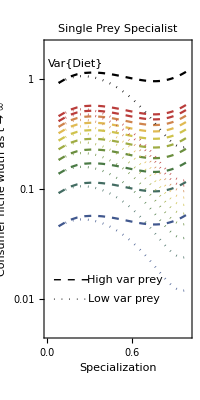
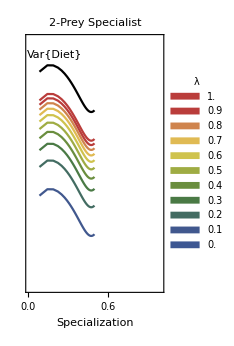

```mathematica
prey1 = 7;
prey2 = 8;
diff = 8;
VarA = VarTablefunc[{prey1,prey1,diff}];VarZTableA = VarA[[1]];VarXTableA = VarA[[2]];
VarB = VarTablefunc[{prey2,prey2,diff}];VarZTableB = VarB[[1]];VarXTableB = VarB[[2]];
VarAB = VarTablefunc[{prey1,prey2,diff}];VarZTableAB = VarAB[[1]];VarXTableAB = VarAB[[2]];
{"A (Dotted)",EX[[prey1]],VarX[[prey1]]}
{"B (Dashed)",EX[[prey2]],VarX[[prey2]]}

MultipleSpecialistPlotdiff8 = 
Row[{
Show[{

ListLogPlot[VarZTableB,PlotStyle->Directive[{Black,Dashed}],PlotRange->{{0,1},{0.005,2}},Joined->True,AspectRatio->2,FrameLabel->{"Specialization","Consumer niche width as t → ∞"},Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},Epilog->Style[Text["Var{Diet}",{0.2,Log@1.4}],12],PlotLabel->"Single Prey Specialist"],
Table[
ListLogPlot[VarXTableB[[i+1]],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->Directive[Dashed,ColorData["DarkRainbow",i/10]],Joined->True],{i,1,10,1}],

ListLogPlot[VarZTableA,PlotStyle->Directive[{Black,Dotted}],PlotRange->{{0,1},{0.005,2}},Joined->True],
Table[
ListLogPlot[VarXTableA[[i+1]],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->Directive[Dotted,ColorData["DarkRainbow",i/10]],Joined->True],{i,1,10,1}],

Graphics[{Thick,Dashed,Line[{{0.05,Log@.015},{0.3,Log@.015}}]}],
Graphics[{Thick,Dotted,Line[{{0.05,Log@.01},{0.3,Log@.01}}]}],

Graphics[Text[Style["High var prey"],{0.55,Log@.015}]],
Graphics[Text["Low var prey",{0.54,Log@.01}]]

},ImageSize->200],

Show[{
ListLogPlot[VarZTableAB,Frame->True,PlotStyle->Black,PlotRange->{{0,1},{0.005,2}},Joined->True,AspectRatio->2,FrameLabel->{"Specialization",""},FrameTicks->{{None,None},{Automatic,None}},Epilog->Style[Text["Var{Diet}",{0.2,Log@1.4}],12],PlotLabel->"2-Prey Specialist"],
ListLogPlot[VarXTableAB,PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->"DarkRainbow",PlotLegends->SwatchLegend[Table[λ,{λ,0,1,0.1}],LegendLabel->"λ",LegendFunction->(#&),LegendMargins->1,LegendLayout->{"ReversedColumn",1}],Joined->True]
},ImageSize->173]
}]
```

```mathematica
Mean[{-15.5,-17.5,-15.6,-15.5,-14.3,-15.4,-15.659999999999997,-15.659999999999997,-15.8,-13.3,-17.5,-16.2}]
```

-15.66

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_nichespecialist.pdf",MultipleSpecialistPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_nichespecialist.pdf

Variance as a function of the dispersion parameter

```mathematica
VarZGamma = Table[
nprey = 12;
EX = {-15.5,-17.5,-15.6,-15.5,-14.3,-15.4,-16.0,-17.0,-15.8,-13.3,-17.5,-16.2};
VarX = {1.00,0.81,0.49,0.81,0.81,0.81,0.25,1.21,0.64,1.21,1.96,1.00};
timebetweenencounters =Table[5,{nprey}];
Dparam = Table[v/timebetweenencounters[[i]],{i,1,12}];
a0 = Total[Dparam];
Ep = N[Dparam/a0];
Varp = N[Table[(Dparam[[i]]*(a0-Dparam[[i]]))/(a0^2*(a0+1)),{i,1,nprey}]];
Covp = N[Table[(-Dparam[[i]]*Dparam[[j]])/(a0^2*(a0+1))Boole[i ≠ j],{i,1,nprey},{j,1,nprey}]];
VarZ = N[Sum[Varp[[i]]*VarX[[i]] + Ep[[i]]^2*VarX[[i]] + EX[[i]]^2*Varp[[i]] + Sum[Covp[[i]][[j]]*EX[[i]]*EX[[j]]Boole[i ≠ j],{j,1,nprey}],{i,1,nprey}]];
VarDiet = (1-Sum[Ep[[i]]^2, {i,1,nprey}])/(nprey*(a0 + 1));
{VarDiet,VarZ},
{v,0.01,1000,0.1}];
VarXGamma = Table[{VarZGamma[[i]][[1]],(λ*VarZGamma[[i]][[2]])/2},{λ,0,1,0.1},{i,1,Length[VarZGamma]}];
```

```mathematica
Total[Ep]
```

1.

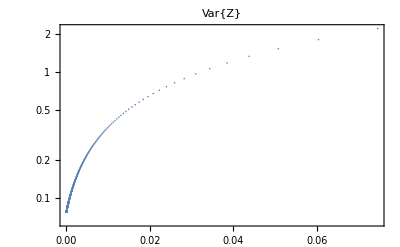

```mathematica
ListLogPlot[VarZGamma,PlotRange->All,Frame->True,PlotLabel->"Var{Z}"]
```

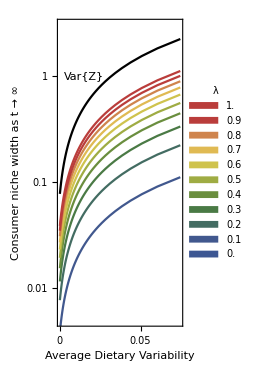

```mathematica
VarSpatialPlot = Show[{
ListLogPlot[VarZGamma,Frame->True,PlotStyle->Black,PlotRange->{All,{0.005,3}},Joined->True,AspectRatio->2,FrameLabel->{"Average Dietary Variability","Consumer niche width as t → ∞"},Epilog->Style[Text["Var{Z}",{0.015,Log@1}],12],FrameTicks->{{All,None},{{0,0.01,0.03,0.05,0.07},None}}],
ListLogPlot[VarXGamma,PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotStyle->"DarkRainbow",PlotLegends->SwatchLegend[Table[λ,{λ,0,1,0.1}],LegendLabel->"λ",LegendFunction->(#&),LegendMargins->1,LegendLayout->{"ReversedColumn",1}],Joined->True]
},ImageSize->193]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_nichegamma.pdf",VarSpatialPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_nichegamma.pdf

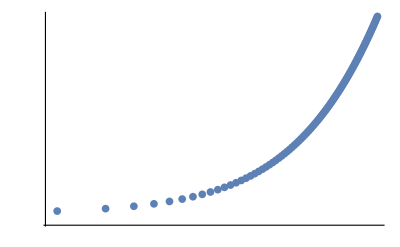

```mathematica
ListLogLogPlot[VarZGamma,Ticks->None]
```

```mathematica
VarXTable3D = Table[{λ,Log[VarZTable[[i]][[1]]],(λ*VarZTable[[i]][[2]])/2},{λ,0,1,0.1},{i,1,Length[VarZTable]}];
```

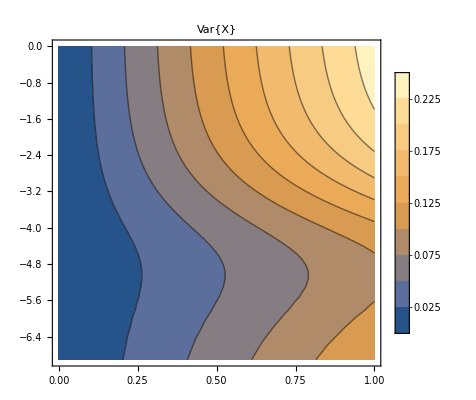

```mathematica
ListContourPlot[Flatten[VarXTable3D,1],PlotRange->All,Frame->True,PlotLabel->"Var{X}",PlotLegends->True]
```

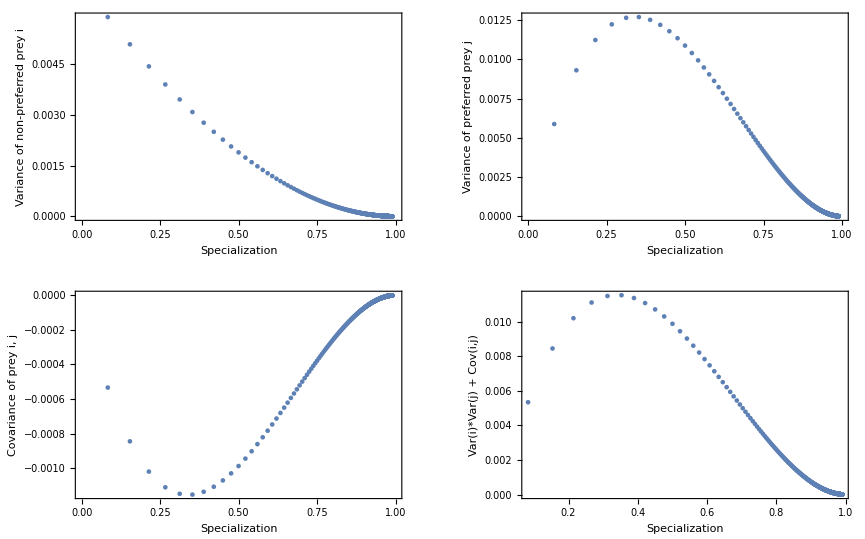

```mathematica
nprey=12;
prey1 = 7;
prey2=7;
VarianceElements=GraphicsGrid[{
{
ListPlot[

VarVector6=Table[
Dparam =Table[1,{nprey}];
Dparam[[prey1]] = a;
Dparam[[prey2]] = a;
a0 = Total[Dparam];
VarVector=N[Table[(Dparam[[i]]*(a0-Dparam[[i]]))/(a0^2*(a0+1)),{i,1,nprey}]];
{a/a0,VarVector[[6]]},
{a,1,1000,1}],PlotRange->{{0,1},All},ImageSize->400,Frame->True,FrameLabel->{"Specialization","Variance of non-preferred prey i"}],
ListPlot[
VarVector7=Table[
Dparam =Table[1,{nprey}];
Dparam[[prey1]] = a;
Dparam[[prey2]] = a;
a0 = Total[Dparam];
VarVector=N[Table[(Dparam[[i]]*(a0-Dparam[[i]]))/(a0^2*(a0+1)),{i,1,nprey}]];
{a/a0,VarVector[[7]]},
{a,1,1000,1}],PlotRange->{{0,1},All},ImageSize->400,Frame->True,FrameLabel->{"Specialization","Variance of preferred prey j"}]},
{
ListPlot[
COV=Table[
Dparam =Table[1,{nprey}];
Dparam[[prey1]] = a;
Dparam[[prey2]] = a;
a0 = Total[Dparam];
COVVector=N[Table[(-Dparam[[i]]*Dparam[[j]])/(a0^2*(a0+1))Boole[i ≠ j],{i,1,nprey},{j,1,nprey}]];
{a/a0,COVVector[[6,7]]},
{a,1,1000,1}],PlotRange->{{0,1},All},ImageSize->400,Frame->True,FrameLabel->{"Specialization","Covariance of prey i, j"}],
ListPlot[Transpose[{VarVector6[[All,1]], VarVector7[[All,2]] + COV[[All,2]]}],PlotRange->All,Frame->True,FrameLabel->{"Specialization","Var(i)*Var(j) + Cov(i,j)"}]}
}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_varianceelements.pdf",VarianceElements]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_varianceelements.pdf